```mathematica
(*Quit[]*)
```

```mathematica
ClearAll["Global`*"];
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[]
```

/run/media/bryan/Resources/Documents/Base/4. 实验/5. 对流斑图/data

```mathematica
<<"~/apps/eclipse-workspace/MathUtils/MathUtils.m"
(*<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,siunitx}"}];*)
Information["Funcs`*"];
autoCollapse[];
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,siunitx}"}];

omarker=Graphics[{Thickness[.2],Disk[]}];
({colors,colorsDefault}
=colorPalette/@{"Scientific","Default"})//Grid
```

RGBColor[0.9, 0.36, 0.054] | RGBColor[0.365248, 0.427802, 0.758297] | RGBColor[0.945109, 0.593901, 0.] | RGBColor[0.645957, 0.253192, 0.685109] | RGBColor[0.285821, 0.56, 0.450773] | RGBColor[0.7, 0.336, 0.] | RGBColor[0.491486, 0.345109, 0.8] | RGBColor[0.71788, 0.568653, 0.] | RGBColor[0.70743, 0.224, 0.542415] | RGBColor[0.287228, 0.490217, 0.664674] | RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636] | RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922] | RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023] | RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854] | RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]
RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.528488, 0.470624, 0.701351] | RGBColor[0.772079, 0.431554, 0.102387] | RGBColor[0.363898, 0.618501, 0.782349] | RGBColor[1, 0.75, 0] | RGBColor[0.647624, 0.37816, 0.614037] | RGBColor[0.571589, 0.586483, 0.] | RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.40082222609352647, 0.5220066643438841, 0.85] | RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142] | RGBColor[0.736782672705901, 0.358, 0.5030266573755369] | RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]

```mathematica
"NO GARBAGE!";
$HistoryLength=0;
```

```mathematica
sheet\
={data2mm,data4mm}\
=Import["data.ods"]⟦All,All,1;;3⟧;
processData[data_,from_]:=Module[{},
{
Round[#⟦1⟧*1000,50],
#⟦1⟧,
#⟦3⟧-#⟦2⟧
}&/@data//Select[
#⟦1⟧≥from&
]
];

{data2mm,data4mm}=processData@@@{
{data2mm,700},
{data4mm,500}
};

hideInfo[HoldForm[{data2mm,data4mm}]]
```

### {data2mm, data4mm}

```mathematica
getImage[sub_,num_,refresh_:False]:=Module[{
filepath=FileNameJoin@{"20190425",sub,ToString[num]<>".bmp"},
exportpath=FileNameJoin@{"pngs",sub,ToString[num]<>".png"}
},
If[!FileExistsQ[filepath],Return[Missing[]]];
If[Not[FileExistsQ[exportpath]]||refresh,
Export[exportpath,Import[filepath]];
];
Import[exportpath]
];

{img2mm,img4mm}=Function[{name,data},
getImage[name,#]&/@data⟦All,1⟧
]@@@{
{"2mm",data2mm},
{"4mm",data4mm}
};

hideInfo[HoldForm[{img2mm,img4mm}]]
```

### {img2mm, img4mm}

```mathematica
SetAttributes[filterMissing,HoldAll]
filterMissing[data_,img_]:={
Pick[data,Not@*MissingQ/@img],
DeleteMissing[img]
};

{
{data2mm,img2mm},
{data4mm,img4mm}
}=filterMissing@@@{
{data2mm,img2mm},
{data4mm,img4mm}
};

hideInfo[filterMissing]
```

### filterMissing

```mathematica
"############################################";
```

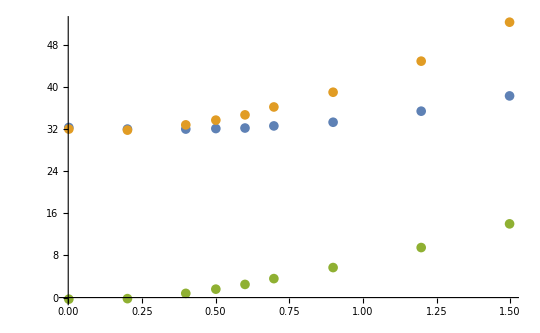

```mathematica
ListPlot[
Evaluate[
Import["data.ods"]⟦2,All,{1,#}⟧&/@{2,3,4}
],
ImageSize->540,
PlotRange->All
]
```

```mathematica
tagImage[img_,amp_,temp_]:=Module[{},
Show[img,
Epilog->Join[
(Inset[
Evaluate@MaTeX[
"\\color{white}"<>" "<>#1
,FontSize->108
,"Preamble"->{"\\usepackage{physics,siunitx,xcolor,bm}"}
]
,#2
,Left
,BaseStyle->{Background->None}
]&)@@@{
{"\\SI{"<>ToString[amp]<>"}{\\A}",Scaled[{.03,.08}]},
{"\\SI{"<>ToString[temp]<>"}{\\celsius}",Scaled[{.03,.20}]}
},{(*ADD EPILOGS HERE*)}
]
]
];

{img2mmTagged,img4mmTagged}=Function[{data,imgSet},
tagImage[imgSet⟦#⟧,data⟦#,2⟧,data⟦#,3⟧]&/@Range[Length[imgSet]]
]@@@{
{data2mm,img2mm},
{data4mm,img4mm}
};
```

```mathematica
{output2mm,output4mm}=GraphicsGrid[
Partition[#,3]
,Spacings->50
]&/@{img2mmTagged,img4mmTagged};
```

```mathematica
exportPlot/@holdItems@{output2mm,output4mm}
```

{plots/output2mm.pdf,plots/output4mm.pdf}